## 稳态传热平面问题

学号：****                姓名：Voldikss

## 一、问题描述

如图一个平板长宽高为 0.2m×0.1m×0.02m，划分为如图所示的网格。材料参数：密度 ρ=7800 kg/m^3，比热 C_p= 500J/(kg · °C)，导热系数 K=50W/(m · °C)。
初始条件为：薄板整体温度100°C。
边界条件为：环境温度 20°C，边 BC 温度恒定为 100°C，边 OAB 换热系数 h=200 W/(m^2·°C)。

请详细推导有限元的整个求解过程，求出该平板内（各个单元）的温度分布。

-Graphics-

## 二、模型推导

### 1. 模型建立

求解区域已经离散为如图标号为1~4的四个单元，将每个单元的节点进行标号。如图所示

-Graphics-

### 2. 求解形函数

温度场插值函数形式为 T(x,y)=α_1+α_2+α_3，其中  α_1、α_2、α_3 为待定系数，三者的值可以根据节点 i、j、k 的坐标值求出。
温度插值函数可以写成 T(x,y)=[N]{T}^e=N_i T_i+N_j T_j+N_k T_k ，其中

N_i=1/(2A)(a_i+b_i x+c_i y), N_j=1/(2A)(a_j+b_j x+c_j y), N_k=1/(2A)(a_k+b_k x+c_k y)，其中
a_i=x_j y_k-x_k y_j, b_i=y_j-y_k, c_i=x_k-x_j
a_j=x_k y_i-x_i y_k, b_j=y_k-y_i, c_j=x_i-x_k
a_k=x_i y_j-x_j y_i, b_k=y_i-y_j, c_k=x_j-x_i

代入各节点坐标计算，可以得到各三角形单元的形函数。

各个点的坐标为：
单元1：i(0, 0), j(0.1, 0.1), k(0, 0.1)
单元2：i(0.1, 0.1), j(0,0), k(0.1, 0)
单元3：i(0.2, 0), j(0.1, 0.1), k(0.1, 0)
单元4：i(0.1, 0.1), j(0.2, 0), k(0.2, 0.1)

使用Wolfram Mathematica 12.0 软件进行计算，代码和运行结果如下所示：

```mathematica
(*计算各单元的形函数*)
Clear["Global`*"]

(*各个点的坐标*)
coordinates = {
{{0,0},{0.1,0.1},{0,0.1}},
{{0.1,0.1},{0,0},{0.1,0}},
{{0.2,0},{0.1,0.1},{0.1,0}},
{{0.1,0.1},{0.2,0},{0.2,0.1}}};

(*计算一个节点的形函数*)
getN[co_]:=Module[{map={"i","j","k"},n,result={}},
	m[n_]:=If[n≤3,Return@n,Return@Mod[n,3]];
    Do[ an = co[[m@(n+1),1]]*co[[m@(n+2),2]]-co[[m@(n+2),1]]*co[[m@(n+1),2]];
		bn = co[[m@(n+1),2]]-co[[m@(n+2),2]];
		cn = co[[m@(n+2),1]]-co[[m@(n+1),1]];
		Nn = 1/(2A)*(an+bn*x+cn*y);
		AppendTo[result,Nn],{n,1,3}];
	Return@result]
	
Do[Echo["单元"<>ToString@n<>"："];Print@getN[coordinates[[n]]],{n,1,4}];
```

单元1：

Null^2 Return[{(0.01-0.1 y)/(2 A),(0.+0.1 x)/(2 A),(0.-0.1 x+0.1 y)/(2 A)}]

单元2：

Null^2 Return[{(0.+0.1 y)/(2 A),(0.01-0.1 x)/(2 A),(0.+0.1 x-0.1 y)/(2 A)}]

单元3：

Null^2 Return[{(-0.01+0.1 x)/(2 A),(0.+0.1 y)/(2 A),(0.02-0.1 x-0.1 y)/(2 A)}]

单元4：

Null^2 Return[{(0.02-0.1 x)/(2 A),(0.01-0.1 y)/(2 A),(-0.02+0.1 x+0.1 y)/(2 A)}]

于是得到各单元的形函数分别为：

单元1：N_i=1/(2A)(0.01-0.1y), N_j=1/(2A)(0.1x),N_k=1/(2A)(-0.1x+0.1y) 
单元2：N_i=1/(2A)(0.1y), N_j=1/(2A)(0.01-0.1x), N_k=1/(2A)(0.1x-0.1y)
单元3：N_i=1/(2A)(-0.01+0.1x), N_j=1/(2A)(0.1y), N_k=1/(2A)(0.02-0.1x-0.1y)
单元4：N_i=1/(2A)(0.02-0.1x), N_j=1/(2A)(0.01-0.1y), N_k=1/(2A)(-0.02+0.1x+0.1y)

其中，A值为每个三角形单元的面积， A=(0.2×0.1)/4=0.005, 1/(2A)=100，代入即可。

### 3. 建立单元刚度矩阵

将温度插值函数代入对应的泛函，并求导得极值条件，内部单元对应的温度刚度矩阵如下：
((∂J^e)/(∂T_i)
(∂J^e)/(∂T_j)
(∂J^e)/(∂T_k))=k/(4A)(b_i^2+c_i^2 | b_i b_j+c_i c_j | b_i b_k+c_i c_k
b_i b_j+c_i c_j | b_j^2+c_j^2 | b_j b_k+c_j c_k
b_i b_k+c_i c_k | b_j b_k+c_j c_k | b_k^2+c_k^2)(T_i
T_j
T_k)=([H]^e[T])^e
另一方面，边界单元需要考虑边界条件：
(0 | 0 | 0
0 | (α s_i)/3 | (α s_i)/6
0 | (α s_i)/6 | (α s_i)/3)(T_i
T_j
T_k)-(0
(α s_i)/2 T_a
(α s_i)/2 T_a)=([H^1]^e[T])^e-[p]^e

两部分相加可得：
(([H]^e+[H^1]^e)[T])^e-{p}^e=0，即([H^-]^e[T])^e=[p]^e

使用 Mathematica 软件计算的过程如下：

```mathematica
(*计算各单元的单元刚度矩阵*)

(*计算一个单元 Subscript[H, 0]*)
getH0[co_]:=Module[{bi,bj,bk,ci,cj,ck,H0,k=50,A=0.005},
	bi=co[[2,2]]-co[[3,2]];
	bj=co[[3,2]]-co[[1,2]];
	bk=co[[1,2]]-co[[2,2]];

	ci=co[[3,1]]-co[[2,1]];
	cj=co[[1,1]]-co[[3,1]];
	ck=co[[2,1]]-co[[1,1]];

	H0=Round/@(k/(4A)({{bi^2+ci^2, bi*bj+ci*cj, bi*bk+ci*ck}, {bi*bj+ci*cj, bj^2+cj^2, bj*bk+cj*ck}, {bi*bk+ci*ck, bj*bk+cj*ck, bk^2+ck^2}}));
	Return@H0]

(*计算一个单元的 Subscript[H, 1]*)
getH1[co_]:=Module[{α=200,si,H1},
	si=√((co[[2,1]]-co[[3,1]])^2+(co[[2,2]]-co[[3,2]])^2);
	H1=Round/@({{0, 0, 0}, {0, (α*si)/3, (α*si)/6}, {0, (α*si)/6, (α*si)/3}});
	Return@H1]

H0s={};
H1s={};
Do[AppendTo[H0s,getH0[coordinates[[n]]]],{n,1,4}];
Do[AppendTo[H1s,getH1[coordinates[[n]]]],{n,1,4}];
Echo@"所有单元的 H0：";
Print@(MatrixForm/@H0s);
Echo@"所有单元的 H1：";
Print@(MatrixForm/@H1s);

Echo@"所有单元的单刚：";
H=H0s+H1s;
H=H0s;
(*2单元和3单元均为边界单元，因此要考虑边界条件*)
H[[2]]=H0s[[2]]+H1s[[2]];
H[[3]]=H0s[[3]]+H1s[[3]];
Print[MatrixForm/@H];
```

所有单元的 H0：

{(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50),(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50),(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50),(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50)}

所有单元的 H1：

{(0 | 0 | 0
0 | 7 | 3
0 | 3 | 7),(0 | 0 | 0
0 | 7 | 3
0 | 3 | 7),(0 | 0 | 0
0 | 7 | 3
0 | 3 | 7),(0 | 0 | 0
0 | 7 | 3
0 | 3 | 7)}

所有单元的单刚：

{(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50),(25 | 0 | -25
0 | 32 | -22
-25 | -22 | 57),(25 | 0 | -25
0 | 32 | -22
-25 | -22 | 57),(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50)}

计算得到各单元的刚度矩阵为：

单元1（内部单元）：[H]=(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50)

单元2（边界单元）：[H]=(25 | 0 | -25
0 | 32 | -22
-25 | -22 | 57)

单元3（边界单元）：[H]=(25 | 0 | -25
0 | 32 | -22
-25 | -22 | 57)

单元4（固定温度边界单元）：[H]=(25 | 0 | -25
0 | 25 | -25
-25 | -25 | 50)

### 4. 建立整体刚度矩阵

使用扩大子阵的方法，将单元刚度矩阵组装为整体刚度矩阵。

```mathematica
Grid[{{" ","O","A","B","C","D","E"},{"O"},{"A"},{"B"},{"C"},{"D"},{"E"}},Frame->All,FrameStyle->{Blue,Thin}]
```

| O | A | B | C | D | E
O |  |  |  |  |  | 
A |  |  |  |  |  | 
B |  |  |  |  |  | 
C |  |  |  |  |  | 
D |  |  |  |  |  | 
E |  |  |  |  |  |

其中各个单元的对应情况为：

单元1：i→O, j→D, k→E, ⇒(OO | OD | OE
DO | DD | DE
EO | ED | EE)
单元2：i→D, j→O, k→A, ⇒(DD | DO | DA
OD | OO | OA
AD | AO | AA)
单元3：i→B, j→D, k→A, ⇒(BB | BD | BA
DB | DD | DA
AB | AD | AA)
单元4：i→D, j→B, k→C, ⇒(DD | DB | DC
BD | BB | BC
CD | CB | CC)

利用 Mathematica，根据上图对应求出各个元素的值，计算总体刚度矩阵 HH：

```mathematica
(*计算总刚*)
OO=H[[1,1,1]]+H[[2,2,2]];
OA=H[[2,2,3]];
OB=0;
OC=0;
OD=H[[1,1,2]]+H[[2,2,1]];
OE=H[[1,1,3]];
AA=H[[2,3,3]]+H[[3,3,3]];
AB=H[[3,3,1]];
AC=0;
AD=H[[2,3,1]]+H[[3,3,2]];
AE=0;
BB=H[[3,1,1]]+H[[4,2,2]];
BC=H[[4,2,3]];
BD=H[[4,2,1]]+H[[3,1,2]];
BE=0;
CC=H[[4,3,3]];
CD=H[[4,3,1]];
CE=0;
DD=H[[2,1,1]]+H[[1,2,2]]+H[[3,2,2]]+H[[4,1,1]];
DE=H[[1,2,3]];
EE=H[[1,3,3]];
HH=({{OO, OA, OB, OC, OD, OE}, {OA, AA, AB, AC, AD, AE}, {OB, AB, BB, BC, BD, BE}, {OC, AC, BC, CC, CD, CE}, {OD, AD, BD, CD, DD, DE}, {OE, AE, BE, CE, DE, EE}});
Echo@"总刚 HH：";
Print@MatrixForm@HH;

p=Transpose[{{200,200,200,0,0,0}}];
Echo@"p：";
Print@MatrixForm@p;
```

总刚 HH：

(57 | -22 | 0 | 0 | 0 | -25
-22 | 114 | -25 | 0 | -47 | 0
0 | -25 | 50 | -25 | 0 | 0
0 | 0 | -25 | 50 | -25 | 0
0 | -47 | 0 | -25 | 107 | -25
-25 | 0 | 0 | 0 | -25 | 50)

p：

(200
200
200
0
0
0)

采用对角元素置1法，将 HH 和 p 整理为

```mathematica
p=p-1000*HH[[All,3]]-1000*HH[[All,4]];
p[[3,1]]=1000;
p[[4,1]]=1000;
Echo@"p：";
Print@MatrixForm@p;

HH[[All,3]]={0,0,1,0,0,0};
HH[[All,4]]={0,0,0,1,0,0};
HH[[3,2]]=0;
HH[[4,5]]=0;
Echo@"总刚HH：";
Print@MatrixForm@HH;
```

p：

(200
25200
1000
1000
25000
0)

总刚HH：

(57 | -22 | 0 | 0 | 0 | -25
-22 | 114 | 0 | 0 | -47 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | -47 | 0 | 0 | 107 | -25
-25 | 0 | 0 | 0 | -25 | 50)

求解矩阵 [H][T]=[p]，即 [T]=[H]^-1[T]：

```mathematica
Dot[Inverse@HH,p]//N//MatrixForm
```

(446.982
554.446
1000.
1000.
599.431
523.207)

将结果化为整数：

```mathematica
Round/@%//MatrixForm
```

(447
554
1000
1000
599
523)

以上结果即为 O→E 每个节点的最终温度值。

### 5. 单元内任一点的温度计算

根据公式 T=N_i T_i+N_j T_j+N_k T_k，代入各个节点的温度值，即可计算出单元内每一点的温度值。

单元1：T_i=446°C, T_j=599°C, T_k=523°C, N_i=100*(0.01-0.1y), N_j=100*(0.1x),N_k=100*(-0.1x+0.1y)
计算得 T^1=223+380 x+385 y

单元2：T_i=599°C, T_j=446°C, T_k=554°C, N_i=100(0.1y), N_j=100(0.01-0.1x), N_k=100(0.1x-0.1y)
计算得 T^2=446+1080 x+450 y

单元3：T_i=1000°C, T_j=599°C, T_k=554°C, N_i=100(-0.01+0.1x), N_j=100(0.1y), N_k=100(0.02-0.1x-0.1y)
计算得 T^3=108+4460 x+450 y

单元4：T_i=599°C, T_j=1000°C, T_k=1000°C, N_i=100(0.02-0.1x), N_j=100(0.01-0.1y), N_k=100(-0.02+0.1x+0.1y)
计算得 T^4=198+4010 x

上述结果中最具有特征的表达式为 T^4，该单元内各店的温度仅与点的横坐标有关，温度随着横坐标的减小而线性减小。而结合题目条件“边BC温度恒定为1000°C”可知，所计算的结果符合该单元的温度变化情况。

使用 Mathematica 软件可以画出四个单元内的温度分布图：

#### 等高线图

```mathematica
T1=223+380 x+385y;
T2=446+1080x+450y;
T3=108+4460x+450y;
T4=198+4010x;
ContourPlot[
    T1*Boole[x≥0&&y≤0.1&&(x-y≤0)]+
	T2*Boole[x≤0.10&&y≥0&&(x-y≥0)]+
	T3*Boole[x≥0.1&&y≥0&&(x+y<0.2)]+
	T4*Boole[x≤0.2&&y≤0.1&&x+y≥0.2],{x,0,0.2},
	{y,0,0.1},
	PlotLegends->Automatic,AspectRatio->1/2,PlotPoints->100,Contours->100,ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics-

#### 密度图

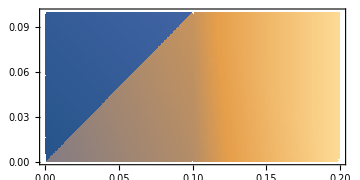

```mathematica
DensityPlot[
    T1*Boole[x≥0&&y≤0.1&&(x-y≤0)]+
	T2*Boole[x≤0.10&&y≥0&&(x-y≥0)]+
	T3*Boole[x≥0.1&&y≥0&&(x+y<0.2)]+
	T4*Boole[x≤0.2&&y≤0.1&&x+y≥0.2],{x,0,0.2},
	{y,0,0.1},
	PlotLegends->Automatic,PlotPoints->100,AspectRatio->1/2,ImageSize->Medium]
```

## 三、软件模拟

利用 Marc 软件对该模型的计算结果进行验证。

### 1. 网格划分

按照 40×20 对网格进行划分如下：

### 2. 模型参数

将密度（7800kg/m^3）、比热（500J/(kg·°C)）、导热系数（50W/(m·°C)）、初始温度（100°C）和环境温度（20°C）等值赋予所有节点。

### 3. 边界条件

添加两个边界条件： 边 BC 温度恒定为 1000 °C，边 O(A)B 换热系数 h=200 W/(m^2·°C)，如图所示

-Graphics-

### 4. 运行结果

#### 4.1 温度云图

可以看到，该温度云图和上面用 Mathematica 绘制的等高线图相似，证明计算的结果是正确的。

#### 4.2 History Plot

上图中 O→E 六个节点的温度随时间变化的情况表示为图像曲线，如图所示：

-Graphics--Graphics-

#### 4.3 结果验证

从 History Plot 可以看出，六个节点最终的温度分别为 O(400°C)、A(500°C)、B(1000°C)、C(1000°C)、D(600°C)、E(500°C)。
将计算得到的结果与模拟值进行对比如下：

```mathematica
Grid[{{"","O","A","B","C","D","E"},{"模拟值",400,500,1000,1000,600,500},{"计算值",447,554,1000,1000,599,523}},Frame->All,FrameStyle->Thin]
```

| O | A | B | C | D | E
模拟值 | 400 | 500 | 1000 | 1000 | 600 | 500
计算值 | 447 | 554 | 1000 | 1000 | 599 | 523

可以看出，其结果较为符合，证明计算结果是正确的。

#### 4.4 是否网格划分更细，该问题可以得到解决？

网格并不是越细越好，太细的网格只会增大计算量，但对结果的精确度的贡献不大，所以一般在选网格数量的时候，要对具体模型选择具体的网格划分数量。